## Definitions

```mathematica
SetDirectory[NotebookDirectory[]];Get["BilliardsDTQW.wl"];
Get["/home/jadeleon/Documents/chaos_meets_channels/Mathematica_packages/QMB.wl"]
```

```mathematica
PlotPr[rTilde_]:=Show[Histogram[rTilde,Automatic,"PDF",PlotRange->{{0.,1.},{-0.01,2.01}},Frame->True,FrameStyle->Directive[Black,FontSize->20],FrameLabel->{HoldForm[r̃], HoldForm[P[r̃]]},ImageSize->400],Plot[27/4*(r+r^2)/((1+r+r^2)^(5/2)),{r,0,1},PlotStyle->Directive[Blue,Thickness[0.015],Dashing[0.03],Opacity[0.75]]],
Plot[2/(1+r)^2,{r,0,1},PlotStyle->Directive[Red,Thickness[0.015],Dashing[0.03],Opacity[0.75]]],
(*The legends in the Epilog are starting here*)Epilog->Inset[LineLegend[{Directive[Red,Thickness[0.015],Dashing[0.03]],Directive[Blue,Thickness[0.015],Dashing[0.03]]},{"Poisson","GOE"},LabelStyle->Directive[Black,FontSize->20],
LegendLayout->"Row", (*Reduce vertical spacing*)
LegendMarkerSize->{40,5} (*Adjusts marker size to reduce spacing*)
],Scaled[{0.61,0.87}]]
(*End of the Legends*)]
```

## Histograma P(r) cambia según la ventana del espectro

```mathematica
(* Import eigenvalues of DTQW's unitary step *)
eigvals=Flatten[ToExpression[Import["eigvals_U_xc_50_alpha_Pi-4_beta_Pi-6.csv","CSV"]]];
```

```mathematica
(* Extract the argument of eigenvalues *)
eigphases=Sort[Mod[Arg[#],2Pi]&/@eigvals];
```

Quitando 5% de cada extremo:

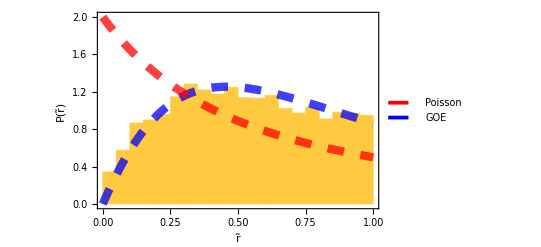

```mathematica
(* Compute the spacing ratios *)
r=Ratios[Differences[eigphases[[459;;-459]]]];

(* Compute the r tilde *)
rTilde=Min/@Transpose[{r,1/r}];

PlotPr[rTilde]
```

Quitando 10% de cada extremo:

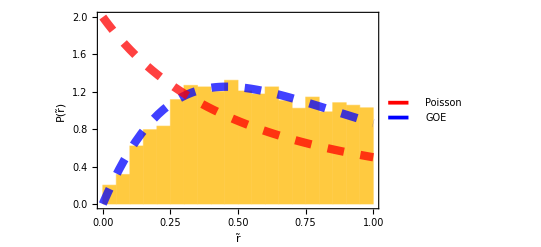

```mathematica
(* Compute the spacing ratios *)
r=Ratios[Differences[eigphases[[918;;-918]]]];

(* Compute the r tilde *)
rTilde=Min/@Transpose[{r,1/r}];

PlotPr[rTilde]
```

Quitando 5-10% de cada extremo (parece que es el mejor):

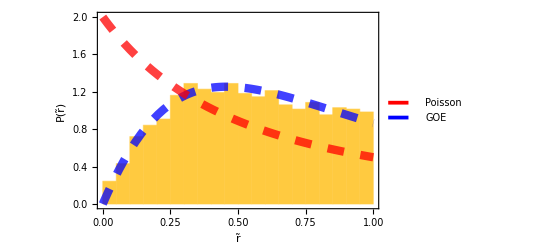

```mathematica
(* Compute the spacing ratios *)
r=Ratios[Differences[eigphases[[650;;-650]]]];

(* Compute the r tilde *)
rTilde=Min/@Transpose[{r,1/r}];

PlotPr[rTilde]
```

Calcular

```mathematica
{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}/.α->Pi/4
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

## P(r) del caso más caótico (?)

```mathematica
xc=50.;
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;
```

```mathematica
(* Shifts *)
ShiftH=HorizontalShift[xc,tags,reversedBasis];
ShiftV=VerticalShift[xc,tags];
```

```mathematica
α=β=Pi/4.;
```

```mathematica
AbsoluteTiming[
(* Coins *)
C1=Coin[α,xc];
C2=Coin[β,xc];

(* DTQW unitary step *)
U=Normal[ShiftH.C2.ShiftV.C1];

(* Eigenvalues of U *)
eigvals=Eigenvalues[U];

(* Spacing ratios *)
Quiet[
eigphases=Sort[Mod[Arg[#],2Pi]&/@eigvals];
r=Ratios[Differences[eigphases[[4000;;-4000]]]];
rTilde=Min/@Transpose[{r,1/r}];
Mean[rTilde]]
]
```

{86.0493,Indeterminate}

```mathematica
(* Spacing ratios *)
Quiet[
eigphases=Sort[Mod[Arg[#],2Pi]&/@eigvals];
r=Ratios[Differences[eigphases[[650;;-650]]]];
rTilde=Min/@Transpose[{r,1/r}];
Mean[rTilde]]
```

Indeterminate

```mathematica
Mean[DeleteCases[DeleteCases[rTilde,_Min],Indeterminate]]
```

0.494163

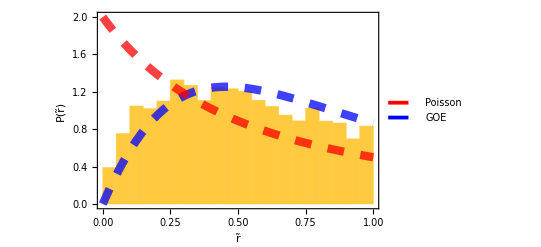

```mathematica
PlotPr[DeleteCases[DeleteCases[rTilde,_Min],Indeterminate]]
```

```mathematica
DeleteCases[DeleteCases[rTilde,_Min],Indeterminate]//Length
```

7806

## Barriendo alpha y beta

```mathematica
ClearAll[α]
{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}/.α->(Pi/4)
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

```mathematica
xc=50.;
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;
```

```mathematica
coinAngles=N[Subdivide[2Pi/3,2Pi,3]]
```

{2.0944,3.49066,4.88692,6.28319}

```mathematica
Subdivide[2Pi/3,2Pi,3]
```

{(2 π)/3,(10 π)/9,(14 π)/9,2 π}

```mathematica
(* Shifts *)
ShiftH=HorizontalShift[xc,tags,reversedBasis];
ShiftV=VerticalShift[xc,tags];
```

```mathematica
eigvals=Eigenvalues[ShiftH.Coin[#,xc].ShiftV.Coin[#,xc]&[coinAngles[[1]]]];
```

Eigenvalues::arh: Because finding 9180 out of the 9180 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

```mathematica
rTildeList={}
```

{}

```mathematica
Do[
(* DTQW unitary step *)
U=Normal[ShiftH.Coin[β,xc].ShiftV.Coin[α,xc]];

(* Eigenvalues of U *)
eigvals=Eigenvalues[U];

AppendTo[rTildeList,{α,β,
(* Spacing ratios *)
Quiet[
eigphases=Sort[Mod[Arg[#],2Pi]&/@eigvals];
r=Ratios[Differences[eigphases[[750;;-750]]]];
rTilde=Min/@Transpose[{r,1/r}];
Mean[rTilde]]
}]
,{α,coinAngles},{β,coinAngles}]
```

```mathematica
Select[rTildeList,Head[#[[3]]]==Real&]
```

{{2.0944,3.49066,0.581342},{3.49066,2.0944,0.581342},{4.88692,3.49066,0.568156}}

```mathematica
rTildeList
```

{{2.0944,2.0944,Indeterminate},{2.0944,3.49066,0.581342},{2.0944,4.88692,Indeterminate},{2.0944,6.28319,Indeterminate},{3.49066,2.0944,0.581342},{3.49066,3.49066,Indeterminate},{3.49066,4.88692,(4360.13+3 Min[0,ComplexInfinity]+3 Min[0.,ComplexInfinity])/7680},{3.49066,6.28319,Indeterminate},{4.88692,2.0944,Indeterminate},{4.88692,3.49066,0.568156},{4.88692,4.88692,Indeterminate},{4.88692,6.28319,Indeterminate},{6.28319,2.0944,Indeterminate},{6.28319,3.49066,Indeterminate},{6.28319,4.88692,Indeterminate},{6.28319,6.28319,Indeterminate}}

```mathematica
ListDensityPlot[Select[rTildeList,Head[#[[3]]]==Real&],InterpolationOrder->0]
```

-Graphics-

## v2 de arxiv

```mathematica
xc=50.;
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;
```

```mathematica
(* Shifts *)
ShiftH=HorizontalShift[xc,tags,reversedBasis];
ShiftV=VerticalShift[xc,tags];
```

```mathematica
ShiftV[[1;;10,1;;10]]//MatrixForm
```

(0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### α=β=π/4

```mathematica
α=Pi/4.;
C1=C2=Chop[KroneckerProduct[IdentityMatrix[Round[DimH[xc]]/2, SparseArray], 
  SparseArray[N[{{Cos[α],Sin[α]},{-Exp[I*Pi/4.]*Sin[α],Exp[I*Pi/4.]*Cos[α]}}]]]]
```

SparseArray[…]

```mathematica
C1[[1;;10,1;;10]]//MatrixForm
```

(0.707107 | 0.707107 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.5-0.5 ⅈ | 0.5+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.707107 | 0.707107 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.5-0.5 ⅈ | 0.5+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.707107 | 0.707107 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.5-0.5 ⅈ | 0.5+0.5 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.707107 | 0.707107 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.5-0.5 ⅈ | 0.5+0.5 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.707107 | 0.707107
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.5-0.5 ⅈ | 0.5+0.5 ⅈ)

```mathematica
U=ShiftH.C2.ShiftV.C1;
```

```mathematica
U//UnitaryMatrixQ
```

True

```mathematica
eigvals=Eigenvalues[Normal[U]];
```

```mathematica
Quiet[
eigphases=Sort[Mod[Arg[#],2Pi]&/@eigvals];
r=Ratios[Differences[eigphases[[750;;-750]]]];
rTilde=Min/@Transpose[{r,1/r}];
Mean[rTilde]]
```

Indeterminate

```mathematica
Mean[Select[rTilde,Head[#]==Real&]]
```

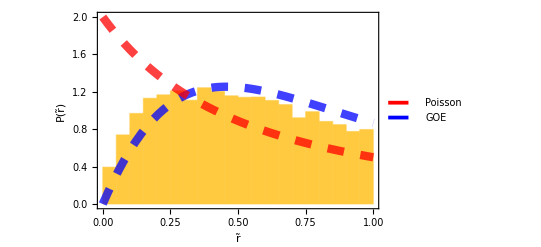

```mathematica
PlotPr[Select[rTilde,Head[#]==Real&]]
```

### α=β=π/3

```mathematica
α=Pi/4.;β=Pi/3.;

C1=Chop[KroneckerProduct[IdentityMatrix[Round[DimH[xc]]/2, SparseArray], 
  SparseArray[N[{{Cos[α],Sin[α]},{-Exp[I*Pi/4.]*Sin[α],Exp[I*Pi/4.]*Cos[α]}}]]]];

C2=Chop[KroneckerProduct[IdentityMatrix[Round[DimH[xc]]/2, SparseArray], 
  SparseArray[N[{{Cos[β],Sin[β]},{-Exp[I*Pi/4.]*Sin[β],Exp[I*Pi/4.]*Cos[β]}}]]]];
```

```mathematica
U=ShiftH.C2.ShiftV.C1
```

SparseArray[…]

```mathematica
U//UnitaryMatrixQ
```

True

```mathematica
eigvals=Eigenvalues[Normal[U]];
```

```mathematica
Export["/home/jadeleon/Documents/chaotic_walks/eigvals_Uv2_xc_50_alpha_Pi-4_beta_Pi-3.csv",eigvals,"CSV"]
```

/home/jadeleon/Documents/chaotic_walks/eigvals_Uv2_xc_50_alpha_Pi-4_beta_Pi-3.csv

```mathematica
(* Import eigenvalues of DTQW's unitary step *)
eigvals=Flatten[ToExpression[Import["eigvals_Uv2_xc_50_alpha_Pi-4_beta_Pi-3.csv","CSV"]]];
```

```mathematica
Quiet[
eigphases=Sort[Mod[Arg[#],2Pi]&/@eigvals];
r=Ratios[Differences[eigphases[[1000;;-1000]]]];
rTilde=Min/@Transpose[{r,1/r}];
Mean[rTilde]]
```

0.548705

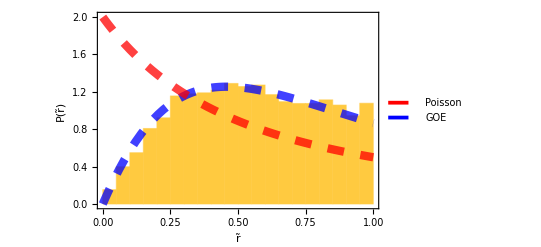

```mathematica
PlotPr[rTilde]
```